## Damping coefficient and asymptote

```mathematica
Mat={
(*96.1 hrs*){A->2.1973509298431977,b->6.594887092325513,c->163.46391704944412},
(*96.2 hrs*){A->3.291621612934128,b->9.7221433282357,c->163.16997101886759},
(*96.3 hrs*){A->2.1332298768257663,b->5.096804704383117,c->162.75414453752123},
(*120.1 hrs*){A->7.063620839003796,b->5.498529842513505,c->180.0611519889982},
(*120.2 hrs*){A->5.181041706861317,b->5.617908553316073,c->178.7017846655297},
(*120.3 hrs*){A->1.7094769646757824,b->5.844658432745917,c->177.81831836095475},
(*120.4 hrs*){A->1.7297530292833092,b->7.493640260247429,c->175.92360524344625},
(*144.1 hrs*){A->2.476862105766373,b->3.5794026797845375,c->173.57578967959756},
(*144.2 hrs*){A->4.1376926022480545,b->6.0130013594923,c->171.29603875982653},
(*144.3 hrs*){A->3.252283543390434,b->5.503602973610219,c->172.56433085930115},
(*144.4 hrs*){A->4.795049055285837,b->6.093999183061484,c->170.23896109644582},
(*144.5 hrs*){A->2.2133692469887483,b->6.363674909172996,c->168.23237892858472},
(*144.6 hrs*){A->3.9459222544455037,b->5.209218956125442,c->168.51565954698737},
(*144.7 hrs*){A->3.8747513299261915,b->11.399715824434914,c->166.190441042818},
(*144.8 hrs*){A->4.5417407398079295,b->10.915290183862963,c->165.9491027677205},
(*168.1 hrs*){A->7.03338466570078,b->6.7617197472699075,c->183.58911393271575},
(*168.2 hrs*){A->6.923579428185456,b->6.670043104630318,c->181.8428568018427},
(*168.4 hrs*){A->2.585829126187223,b->6.476042330628748,c->178.67177896991643},
(*168.5 hrs*){A->4.220413765518654,b->4.4999703057496445,c->177.2294401370988},
(*168.6 hrs*){A->4.795094907851771,b->12.206611358026839,c->175.72354533034684}
};
```

```mathematica
clean=Values/@Mat;
Export["Relaxation.csv",clean]
```

Relaxation.csv

Histograms of damping coefficient (left) and asymptote angle in degrees (right).

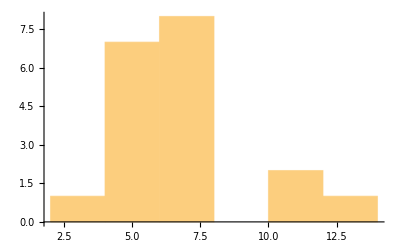
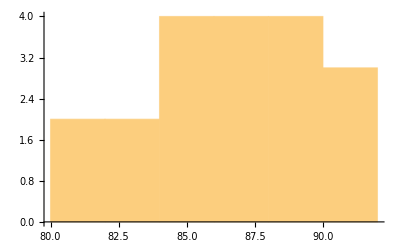

```mathematica
{Histogram[Table[b/.Mat[[n, 2]], {n, 1, Length[Mat],1}], 5],Histogram[Table[(c/.Mat[[n, 3]])/2 , {n, 1, Length[Mat],1}], 5]}
```

Damping coefficient as a function of aging in hrs.

```mathematica
index = {96.1,96.2,96.3 ,120.1 ,120.2,120.3 ,120.4,144.1 ,144.2,144.3,144.4,144.5 ,144.6,144.7,144.8,168.1,168.2,168.4,168.5,168.6};
F = Table[{index[[i]], A/.Mat[[i,1]], b/.Mat[[i,2]],c/.Mat[[i,3]]},{i, 1, 19}]
```

{{96.1,2.19735,6.59489,163.464},{96.2,3.29162,9.72214,163.17},{96.3,2.13323,5.0968,162.754},{120.1,7.06362,5.49853,180.061},{120.2,5.18104,5.61791,178.702},{120.3,1.70948,5.84466,177.818},{120.4,1.72975,7.49364,175.924},{144.1,2.47686,3.5794,173.576},{144.2,4.13769,6.013,171.296},{144.3,3.25228,5.5036,172.564},{144.4,4.79505,6.094,170.239},{144.5,2.21337,6.36367,168.232},{144.6,3.94592,5.20922,168.516},{144.7,3.87475,11.3997,166.19},{144.8,4.54174,10.9153,165.949},{168.1,7.03338,6.76172,183.589},{168.2,6.92358,6.67004,181.843},{168.4,2.58583,6.47604,178.672},{168.5,4.22041,4.49997,177.229}}

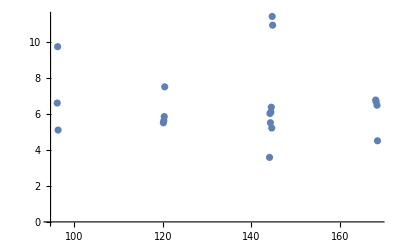

```mathematica
ListPlot[Table[{F[[i, 1]], F[[i, 3]]}, {i, 1, 19}]]
```

## Natural frequency

```mathematica
MatFreq={
(*96.1 hrs*)4.8,
(*96.2 hrs*)5.052631576819945,
(*96.3 hrs*)4.49999999775,
(*120.1 hrs*)5.052631576819945,
(*120.2 hrs*)5.052631576819944,
(*120.3 hrs*)5.052631576819944,
(*120.4 hrs*)4.800000001920001,
(*144.1 hrs*)5.333333333333334,
(*144.2 hrs*)4.80000000192,
(*144.3 hrs*)5.333333333333334,
(*144.4 hrs*)4.571428571428571,
(*144.5 hrs*)5.333333333333334,
(*144.6 hrs*)4.800000001920001,
(*144.7 hrs*)4.7999999961599995,
(*144.8 hrs*)3.8399999987711997,
(*168.1 hrs*)5.052631583202216,
(*168.2 hrs*)5.052631583202216,
(*168.4 hrs*)5.052631583202217,
(*168.5 hrs*)4.571428571428571,
(*168.6 hrs*)4.79999999616
};
```

```mathematica
Export["ObsFrequency.csv",MatFreq]
```

ObsFrequency.csv

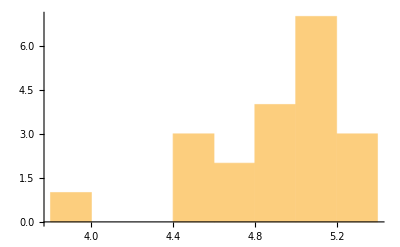

```mathematica
Histogram[Table[MatFreq[[n]], {n, 1, Length[MatFreq],1}], 10]
```

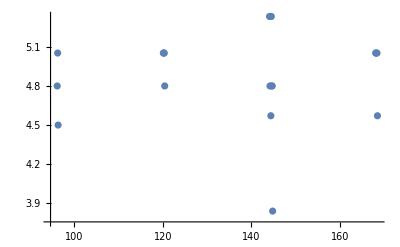

```mathematica
FFreq = Table[{index[[i]], MatFreq[[i]]},{i, 1, 19}];
ListPlot[Table[{FFreq[[i, 1]], FFreq[[i, 2]]}, {i, 1, 19}]]
```

```mathematica
N[Sqrt[(2Pi )^2 6^2 + 6^2]]
```

38.1736

```mathematica
N[2Pi 6]
```

37.6991

```mathematica
38.17359078940397/(2Pi)
```

6.07552

```mathematica
37.69911184307752/(2Pi)
```

6.